```mathematica
PolLagriIter[A_,f_,B_]:= Module[{i,j,n,Pol = 0, Usar = {}},
Usar = Intersection[A,B];
n = Length[Usar];

For[i=1,i≤ n, i++, 
L = 1;
For[j=1,j≤ n, j++,
If[j≠ i,
L = L ×(x - Usar[[j]])/(Usar[[i]] - Usar[[j]])
];
];
Pol = Pol + L f[Usar[[i]]];
];
Print["El poinomio de Lagrenge que pasa por los puntos ", Usar, " corresponde a ", Simplify[Pol], ", con grafica: "];
PolinomioLagrange:= Simplify[Pol];
Plot[{f[x],PolinomioLagrange}, {x, A[[1]] - 1, A[[n]] + 1}, PlotLegends->"Expressions"]
];
```

El poinomio de Lagrenge que pasa por los puntos {2,3,6} corresponde a 36-36 x+11 x^2, con grafica:

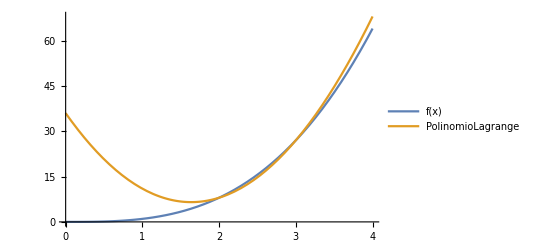

```mathematica
A = {1,2,3,4,6};
B = {2,3,6};
f[x_]:= x^3;
PolLagriIter[A,f,B]
```